```mathematica
a=InputField["x", x]
```

InputField[x,x]

```mathematica
i=Input["Please input an integer value that is equal to the number of charges desired"]
```

4

```mathematica
f[i_]:=InputString["Please write the name of the" i "th charge particle"]
```

```mathematica
f[1]
```

```mathematica
f[i_]:=InputString["Please write the name of the",i,"th charge particle"]
```

```mathematica
f[1]
```

InputString::argt: InputString called with 3 arguments; 0 or 1 arguments are expected.

InputString[Please write the name of the,1,th charge particle]

```mathematica
f[i_]:=InputString[StringForm["Please write the name of charged particle number ``." ,i]]
```

```mathematica
f[1]
```

```mathematica
components=Table[f[x],{x,1,i}]
```

{charge1,charge2,charge3,charge4}

```mathematica
∈
```

```mathematica
D
```

D

```mathematica
components
```

{f[x],f[x],f[x],f[x]}

```mathematica
components=Table[f[x],{x,1,i}]
```

{a,b,c,d}

```mathematica
components
```

{a,b,c,d}

WolframAlphaQueryResults

1 | noun | an abstract part of something
2 | noun | something determined in relation to something that includes it
3 | noun | an artifact that is one of the individual parts of which a composite entity is made up; especially a part that can be separated from or attached to a system

WolframAlphaQueryNoResults

```mathematica
"a" ∈ "Modelica.UserConference"
```

a∈Modelica.UserConference

```mathematica
componentNames=components
```

{a,b,c,d}

```mathematica
componentNames
```

{a,b,c,d}

```mathematica
componentNames[1]
```

{a,b,c,d}[1]

```mathematica
componentNames[[1]]
```

a

```mathematica
g[i_]:=StringForm[componentNames]∈"EFieldLine.Components.CParticle"
```

```mathematica
g[1]
```

StringForm::string: String expected at position 1 in StringForm[{"a", "b", "c", "d"}].

StringForm[{a,b,c,d}]∈EFieldLine.Components.CParticle

```mathematica
g[i_]:=StringForm[componentNames]∈"EFieldLine.Components.CParticle"
```

```mathematica
g[i_]:=StringForm[componentNames[[i]]]∈"EFieldLine.Components.CParticle"
```

```mathematica
g[1]
```

a∈EFieldLine.Components.CParticle

```mathematica
componentNames=Table[f[x],{x,1,i}]
```

{a,b,v,f}

```mathematica
components=Table[g[x],{x,1,i}]
```

{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle}

```mathematica
h[i_]:=componentNames[[i]]<>".field"-> "tparticle1.E"
```

```mathematica
h[1]
```

a.field→tparticle1.E

```mathematica
connections=Table[h[x],{x,1,i}]
```

{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}

```mathematica
Append[components,"tparticle1" ∈"EFieldLine.Components.TParticle"]
```

{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
model=WSMConnectComponents["TrialFieldLine", components,connections]
```

WSMConnectComponents[TrialFieldLine,{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle},{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}]

```mathematica
Needs["WSMLink`"]
```

WSMConnectComponents::shdw: Symbol "WSMConnectComponents" appears in multiple contexts {"WSMLink`", "Global`"}; definitions in context "WSMLink`" may shadow or be shadowed by other definitions.

```mathematica
model=WSMConnectComponents["TrialFieldLine", components,connections]
```

WSMConnectComponentsString::nosup: Found unsupported expression: "a".

WSMConnectComponentsString::nosup: Found unsupported expression: "b".

WSMConnectComponentsString::nosup: Found unsupported expression: "v".

General::stop: Further output of WSMConnectComponentsString :: nosup will be suppressed during this calculation.

WSMConnectComponents[TrialFieldLine,{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle},{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}]

```mathematica
mmodel=WSMConnectComponents["SimpleCircuit",components,connections]
```

WSMConnectComponentsString::nosup: Found unsupported expression: "a".

WSMConnectComponentsString::nosup: Found unsupported expression: "b".

WSMConnectComponentsString::nosup: Found unsupported expression: "v".

General::stop: Further output of WSMConnectComponentsString :: nosup will be suppressed during this calculation.

WSMConnectComponents[SimpleCircuit,{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle},{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}]

```mathematica
Quit
```

```mathematica
Needs["WSMLink`"]
```

```mathematica
mmodel=WSMConnectComponents["SimpleCircuit",components,connections]
```

WSMConnectComponents[SimpleCircuit,components,connections]

```mathematica
>> WSMLink`
```

Syntax::tsntxi: ">> WSMLink`" is incomplete; more input is needed.""

```mathematica
<< WSMLink`
```

WSMLink::ald: SystemModeler Link is already loaded.

$Aborted

```mathematica
Get["WSMLink`"]
```

WSMLink::ald: SystemModeler Link is already loaded.

$Aborted

```mathematica
Quit
```

```mathematica
Needs["WSMLink`"]
```

```mathematica
mmodel=WSMConnectComponents["SimpleCircuit",components,connections]
```

WSMConnectComponents[SimpleCircuit,components,connections]

```mathematica
WSMModelData[mmodel]
```

WSMModelData[WSMConnectComponents[SimpleCircuit,components,connections]]

```mathematica
Quit
```

```mathematica
Needs["WSMLink`"]
```

```mathematica
mmodel=WSMConnectComponents["SimpleCircuit",components,connections]
```

WSMConnectComponents[SimpleCircuit,components,connections]

```mathematica
components
```

```mathematica
components={"a.field"->"tparticle1.E","b.field"->"tparticle1.E","v.field"->"tparticle1.E","f.field"->"tparticle1.E"}
```

{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}

```mathematica
connections={"a.field"->"tparticle1.E","b.field"->"tparticle1.E","v.field"->"tparticle1.E","f.field"->"tparticle1.E"}
```

```mathematica
{"a.field"->"tparticle1.E","b.field"->"tparticle1.E","v.field"->"tparticle1.E","f.field"->"tparticle1.E"}
```

```mathematica
components={"a"∈"EFieldLine.Components.CParticle","b"∈"EFieldLine.Components.CParticle","v"∈"EFieldLine.Components.CParticle","f"∈"EFieldLine.Components.CParticle","tparticle1"∈"EFieldLine.Components.TParticle"}
```

```mathematica
{"a"∈"EFieldLine.Components.CParticle","b"∈"EFieldLine.Components.CParticle","v"∈"EFieldLine.Components.CParticle","f"∈"EFieldLine.Components.CParticle","tparticle1"∈"EFieldLine.Components.TParticle"}
```

```mathematica
model=WSMConnectComponents["Trial",components,connections]
```

WSMConnectComponentsString::nosup: Found unsupported expression: "a".

WSMConnectComponentsString::nosup: Found unsupported expression: "b".

WSMConnectComponentsString::nosup: Found unsupported expression: "v".

General::stop: Further output of WSMConnectComponentsString :: nosup will be suppressed during this calculation.

WSMConnectComponents[Trial,{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle},{a.field→tparticle1.E,b.field→tparticle1.E,v.field→tparticle1.E,f.field→tparticle1.E}]

```mathematica
a
```

a

```mathematica
f
```

f

```mathematica
tparticle1
```

tparticle1

```mathematica
Information[tparticle1]
```

Global`tparticle1

```mathematica
componentss={"R"∈"Modelica.Electrical.Analog.Basic.Resistor","L"∈"Modelica.Electrical.Analog.Basic.Inductor","AC"∈"Modelica.Electrical.Analog.Sources.SineVoltage","G"∈"Modelica.Electrical.Analog.Basic.Ground"};
```

```mathematica
connectionss={"G.p"->"AC.n","AC.p"->"L.n","L.p"->"R.n","R.p"->"AC.n"};
```

```mathematica
mmodel=WSMConnectComponents["SimpleCircuit",componentss,connectionss]
```

-Graphics-

```mathematica
components={"a"∈"EFieldLine.Components.CParticle","b"∈"EFieldLine.Components.CParticle","v"∈"EFieldLine.Components.CParticle","f"∈"EFieldLine.Components.CParticle","tparticle1"∈"EFieldLine.Components.TParticle"}
```

{a∈EFieldLine.Components.CParticle,b∈EFieldLine.Components.CParticle,v∈EFieldLine.Components.CParticle,f∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
model=WSMConnectComponents["Trial",components,connections]
```

-Graphics-

```mathematica
InputString["write the phrase \"hello world\""]
```

hello world

```mathematica
j[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".q"-> Input[StringForm["Please enter the (integer) value for the charge of particle ``.",i]]
```

```mathematica
i
```

4

```mathematica
componentNames={"a","b","v","f"}
```

{a,b,v,f}

```mathematica
chargeValue=Table[j[x],{x,1,i}]
```

{a.q→1,b.q→3,v.q→2,f.q→1}

```mathematica
WSMSetValues[model,Table[j[x],{x,1,i}]]
```

{a.q→1,b.q→3,v.q→2,f.q→1}

```mathematica
k[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".x"-> Input[StringForm["Please enter the x coordinate for the charge of particle ``.",i]]
```

```mathematica
k[1]
```

a.x→0

```mathematica
WSMSetValues[model,Table[k[x],{x,1,i}]]
```

StringJoin::string: String expected at position 1 in $Canceled <> ".x".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

WSMSetValues[-Graphics-,{a.x→$Canceled,$Canceled<>.x→$Canceled,$Canceled<>.x→$Canceled,$Canceled<>.x→$Canceled}]

```mathematica
WSMSetValues[model,Table[j[x],{x,1,i}]]
```

{a.q→1,b.q→1,v.q→1,f.q→-1}

```mathematica
2*Sqrt[3]
```

2 √3

```mathematica
Sqrt[3]
```

√3

```mathematica
N[√3]
```

1.73205

```mathematica
WSMSetValues[model,Table[k[x],{x,1,i}]]
```

{a.x→-1.73205,b.x→1.73205,v.x→0,f.x→0}

```mathematica
m[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".y"-> Input[StringForm["Please enter the y coordinate for the charge of particle ``.",i]]
```

```mathematica
WSMSetValues[model,Table[m[x],{x,1,i}]]
```

{a.y→-1,b.y→-1,v.y→2,f.y→0}

```mathematica
WSMModelData[model]
```

WSMModelData[-Graphics-]

```mathematica
WSMModelData["Trial"]
```

-Graphics-

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["EFieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
mR1 = multipleEfieldLineSims[0,2,0.25,20];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

WSMSimulate::bldl: "Error: Error building simulator. Build log: \\\"/usr/bin/g++\\\"  -m64 -fPIC    -I\\\".\\\"  -I\\\"/Applications/SystemModeler.app/Contents/MacOS/../include\\\"  -I\\\"/Applicati" … "_41934_84071847491647904899.cpp wsml_EFieldRunner_lsim_6219_41934_84071847491647904899_functions.cpp wsml_EFieldRunner_lsim_6219_41934_84071847491647904899.makefile"

WSMSimulate::bldl: "Undefined symbols for architecture x86_64:"

WSMSimulate::bldl: "\\\"std::string::find_last_of(char, unsigned long) const\\\", referenced from:"

General::stop: Further output of WSMSimulate :: bldl will be suppressed during this calculation.

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

General::stop: Further output of WSMSimulate :: bld will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{xR1 ⟦ 1 ⟧[x], yR1 ⟦ 1 ⟧[x]}, {x, 0, dmR1SimTime[1]}], ParametricPlot[{xR1 ⟦ 2 ⟧[x], yR1 ⟦ 2 ⟧[x]}, {x, 0, dmR1SimTime[2]}], ParametricPlot[{xR1 ⟦ 3 ⟧[x], yR1 ⟦ 3 ⟧[x]}, {x, 0, dmR1SimTime[3]}], « 16 », ParametricPlot[{xR1 ⟦ 20 ⟧[x], yR1 ⟦ 20 ⟧[x]}, {x, 0, dmR1SimTime[20]}], ParametricPlot[{xR1 ⟦ 21 ⟧[x], yR1 ⟦ 21 ⟧[x]}, {x, 0, dmR1SimTime[21]}]}, PlotRange → All].

Show[{ParametricPlot[{xR1⟦1⟧[x],yR1⟦1⟧[x]},{x,0,dmR1SimTime[1]}],ParametricPlot[{xR1⟦2⟧[x],yR1⟦2⟧[x]},{x,0,dmR1SimTime[2]}],ParametricPlot[{xR1⟦3⟧[x],yR1⟦3⟧[x]},{x,0,dmR1SimTime[3]}],ParametricPlot[{xR1⟦4⟧[x],yR1⟦4⟧[x]},{x,0,dmR1SimTime[4]}],ParametricPlot[{xR1⟦5⟧[x],yR1⟦5⟧[x]},{x,0,dmR1SimTime[5]}],ParametricPlot[{xR1⟦6⟧[x],yR1⟦6⟧[x]},{x,0,dmR1SimTime[6]}],ParametricPlot[{xR1⟦7⟧[x],yR1⟦7⟧[x]},{x,0,dmR1SimTime[7]}],ParametricPlot[{xR1⟦8⟧[x],yR1⟦8⟧[x]},{x,0,dmR1SimTime[8]}],ParametricPlot[{xR1⟦9⟧[x],yR1⟦9⟧[x]},{x,0,dmR1SimTime[9]}],ParametricPlot[{xR1⟦10⟧[x],yR1⟦10⟧[x]},{x,0,dmR1SimTime[10]}],ParametricPlot[{xR1⟦11⟧[x],yR1⟦11⟧[x]},{x,0,dmR1SimTime[11]}],ParametricPlot[{xR1⟦12⟧[x],yR1⟦12⟧[x]},{x,0,dmR1SimTime[12]}],ParametricPlot[{xR1⟦13⟧[x],yR1⟦13⟧[x]},{x,0,dmR1SimTime[13]}],ParametricPlot[{xR1⟦14⟧[x],yR1⟦14⟧[x]},{x,0,dmR1SimTime[14]}],ParametricPlot[{xR1⟦15⟧[x],yR1⟦15⟧[x]},{x,0,dmR1SimTime[15]}],ParametricPlot[{xR1⟦16⟧[x],yR1⟦16⟧[x]},{x,0,dmR1SimTime[16]}],ParametricPlot[{xR1⟦17⟧[x],yR1⟦17⟧[x]},{x,0,dmR1SimTime[17]}],ParametricPlot[{xR1⟦18⟧[x],yR1⟦18⟧[x]},{x,0,dmR1SimTime[18]}],ParametricPlot[{xR1⟦19⟧[x],yR1⟦19⟧[x]},{x,0,dmR1SimTime[19]}],ParametricPlot[{xR1⟦20⟧[x],yR1⟦20⟧[x]},{x,0,dmR1SimTime[20]}],ParametricPlot[{xR1⟦21⟧[x],yR1⟦21⟧[x]},{x,0,dmR1SimTime[21]}]},PlotRange→All]

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["Trial", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
mR1 = multipleEfieldLineSims[0,2,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```

WSMSimulate::dend: Using default simulation time. Consider giving a simulation interval or configuring model experiment settings.

WSMSimulate::bld: Failed to build model "Trial".

WSMSimulate::bldl: "Error: Error building simulator. Build log: \\\"/usr/bin/g++\\\"  -m64 -fPIC    -I\\\".\\\"  -I\\\"/Applications/SystemModeler.app/Contents/MacOS/../include\\\"  -I\\\"/Applicati" … "wsml_Trial_lsim_6219_41934_840718474998173437.cpp wsml_Trial_lsim_6219_41934_840718474998173437_functions.cpp wsml_Trial_lsim_6219_41934_840718474998173437.makefile"

WSMSimulate::bldl: "Undefined symbols for architecture x86_64:"

WSMSimulate::bldl: "\\\"std::string::find_last_of(char, unsigned long) const\\\", referenced from:"

General::stop: Further output of WSMSimulate :: bldl will be suppressed during this calculation.

WSMSimulate::dend: Using default simulation time. Consider giving a simulation interval or configuring model experiment settings.

WSMSimulate::bld: Failed to build model "Trial".

WSMSimulate::dend: Using default simulation time. Consider giving a simulation interval or configuring model experiment settings.

General::stop: Further output of WSMSimulate :: dend will be suppressed during this calculation.

WSMSimulate::bld: Failed to build model "Trial".

General::stop: Further output of WSMSimulate :: bld will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{xR1 ⟦ 1 ⟧[x], yR1 ⟦ 1 ⟧[x]}, {x, 0, dmR1SimTime[1]}], ParametricPlot[{xR1 ⟦ 2 ⟧[x], yR1 ⟦ 2 ⟧[x]}, {x, 0, dmR1SimTime[2]}], ParametricPlot[{xR1 ⟦ 3 ⟧[x], yR1 ⟦ 3 ⟧[x]}, {x, 0, dmR1SimTime[3]}], « 6 », ParametricPlot[{xR1 ⟦ 10 ⟧[x], yR1 ⟦ 10 ⟧[x]}, {x, 0, dmR1SimTime[10]}], ParametricPlot[{xR1 ⟦ 11 ⟧[x], yR1 ⟦ 11 ⟧[x]}, {x, 0, dmR1SimTime[11]}]}, PlotRange → All].

Show[{ParametricPlot[{xR1⟦1⟧[x],yR1⟦1⟧[x]},{x,0,dmR1SimTime[1]}],ParametricPlot[{xR1⟦2⟧[x],yR1⟦2⟧[x]},{x,0,dmR1SimTime[2]}],ParametricPlot[{xR1⟦3⟧[x],yR1⟦3⟧[x]},{x,0,dmR1SimTime[3]}],ParametricPlot[{xR1⟦4⟧[x],yR1⟦4⟧[x]},{x,0,dmR1SimTime[4]}],ParametricPlot[{xR1⟦5⟧[x],yR1⟦5⟧[x]},{x,0,dmR1SimTime[5]}],ParametricPlot[{xR1⟦6⟧[x],yR1⟦6⟧[x]},{x,0,dmR1SimTime[6]}],ParametricPlot[{xR1⟦7⟧[x],yR1⟦7⟧[x]},{x,0,dmR1SimTime[7]}],ParametricPlot[{xR1⟦8⟧[x],yR1⟦8⟧[x]},{x,0,dmR1SimTime[8]}],ParametricPlot[{xR1⟦9⟧[x],yR1⟦9⟧[x]},{x,0,dmR1SimTime[9]}],ParametricPlot[{xR1⟦10⟧[x],yR1⟦10⟧[x]},{x,0,dmR1SimTime[10]}],ParametricPlot[{xR1⟦11⟧[x],yR1⟦11⟧[x]},{x,0,dmR1SimTime[11]}]},PlotRange→All]

WSMSimulate::dend: Using default simulation time. Consider giving a simulation interval or configuring model experiment settings.

General::stop: Further output of WSMSimulate :: dend will be suppressed during this calculation.

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.06536"

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

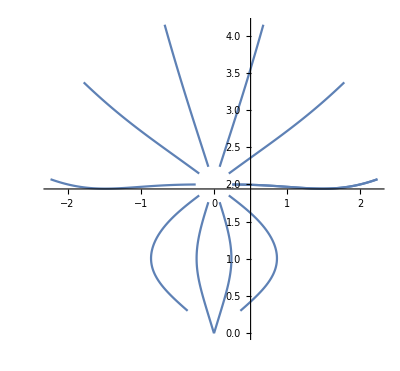

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["Trial", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
mR1 = multipleEfieldLineSims[0,2,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```

```mathematica
mR1 = multipleEfieldLineSims[0,2,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```

WSMSimulate::tint: Wrong time specification: start time is larger than or equal to stop time.

General::stop: Further output of WSMSimulate :: tint will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

Part::partw: Part 2 of $Failed["SimulationInterval"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[2]} is not a machine-sized real number.

ParametricPlot::plln: Limiting value $Failed["SimulationInterval"] ⟦ 2 ⟧ in {x, 0, dmR1SimTime[3]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot :: plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[{xR1 ⟦ 1 ⟧[x], yR1 ⟦ 1 ⟧[x]}, {x, 0, dmR1SimTime[1]}], ParametricPlot[{xR1 ⟦ 2 ⟧[x], yR1 ⟦ 2 ⟧[x]}, {x, 0, dmR1SimTime[2]}], ParametricPlot[{xR1 ⟦ 3 ⟧[x], yR1 ⟦ 3 ⟧[x]}, {x, 0, dmR1SimTime[3]}], « 6 », ParametricPlot[{xR1 ⟦ 10 ⟧[x], yR1 ⟦ 10 ⟧[x]}, {x, 0, dmR1SimTime[10]}], ParametricPlot[{xR1 ⟦ 11 ⟧[x], yR1 ⟦ 11 ⟧[x]}, {x, 0, dmR1SimTime[11]}]}, PlotRange → All].

Show[{ParametricPlot[{xR1⟦1⟧[x],yR1⟦1⟧[x]},{x,0,dmR1SimTime[1]}],ParametricPlot[{xR1⟦2⟧[x],yR1⟦2⟧[x]},{x,0,dmR1SimTime[2]}],ParametricPlot[{xR1⟦3⟧[x],yR1⟦3⟧[x]},{x,0,dmR1SimTime[3]}],ParametricPlot[{xR1⟦4⟧[x],yR1⟦4⟧[x]},{x,0,dmR1SimTime[4]}],ParametricPlot[{xR1⟦5⟧[x],yR1⟦5⟧[x]},{x,0,dmR1SimTime[5]}],ParametricPlot[{xR1⟦6⟧[x],yR1⟦6⟧[x]},{x,0,dmR1SimTime[6]}],ParametricPlot[{xR1⟦7⟧[x],yR1⟦7⟧[x]},{x,0,dmR1SimTime[7]}],ParametricPlot[{xR1⟦8⟧[x],yR1⟦8⟧[x]},{x,0,dmR1SimTime[8]}],ParametricPlot[{xR1⟦9⟧[x],yR1⟦9⟧[x]},{x,0,dmR1SimTime[9]}],ParametricPlot[{xR1⟦10⟧[x],yR1⟦10⟧[x]},{x,0,dmR1SimTime[10]}],ParametricPlot[{xR1⟦11⟧[x],yR1⟦11⟧[x]},{x,0,dmR1SimTime[11]}]},PlotRange→All]

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 12.3483"

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

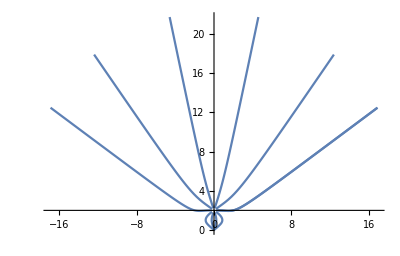

```mathematica
mR1 = multipleEfieldLineSims[0,2,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results=Table[EpPlot[i],{i,1,dmR1}];
Show[results,PlotRange->All]
```

```mathematica
Show[%98,ImageSize->Full]
```

-Graphics-

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.28542"

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

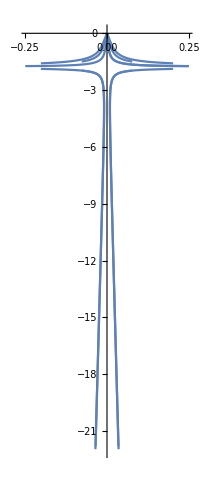

```mathematica
mR1 = multipleEfieldLineSims[0,-1.732050807568877,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results2=Table[EpPlot[i],{i,1,dmR1}];
Show[results2,PlotRange->All]
```

```mathematica
Show[%107,ImageSize->Full]
```

-Graphics-

```mathematica
p=1.732050807568877
```

1.73205

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.67388"

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

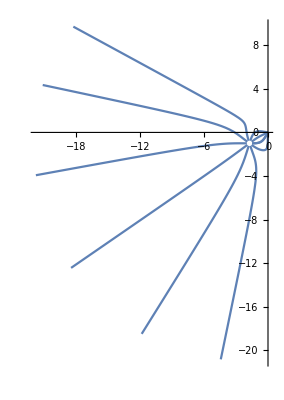

```mathematica
mR1 = multipleEfieldLineSims[-1.732050807568877,-1,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results2=Table[EpPlot[i],{i,1,dmR1}];
Show[results2,PlotRange->All]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 10.6977"

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Trial" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

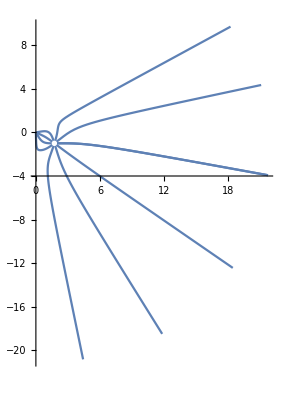

```mathematica
mR1 = multipleEfieldLineSims[1.732050807568877,-1,0.25,10];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results3=Table[EpPlot[i],{i,1,dmR1}];
Show[results3,PlotRange->All]
```

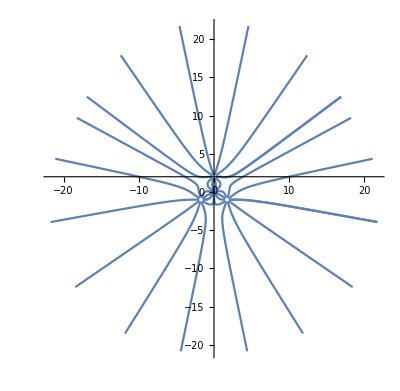

```mathematica
Show[results,results2,results3,PlotRange->All]
```

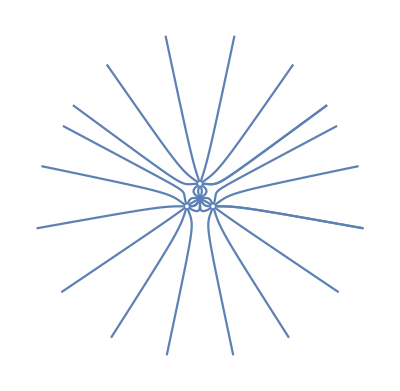

```mathematica
Show[%126,Axes->False]
```

```mathematica
Needs["WSMLink`"]
```